## EELE 582 Optical Design Homework 5 Roy Smart

## Problem 1

```mathematica
Clear["Global`*"]
```

#### Third-order coma is given by the expression

```mathematica
Wc = W131 H ρ^3 Cos[ϕ];
```

#### The transverse ray aberration is found using the relation

```mathematica
p2c = {ρ-> √(x^2+y^2),ϕ-> ArcTan[x,y]};
c2p =  {x-> ρ Sin[ϕ],y-> ρ Cos[ϕ]} ;
T[W_]:= -(R/(n r))Grad[(W /. p2c),{x,y}] /. c2p //FullSimplify
```

#### Plug our expression for coma into the transverse ray aberration function

```mathematica
(Tc[ρ_,ϕ_] = T[Wc]) //Framed
```

{(H R W131 ρ^2 (-2+Cos[2 ϕ]))/(n r),-(2 H R W131 ρ^2 Cos[ϕ] Sin[ϕ])/(n r)}

#### Create list of pupil points in polar coordinates

```mathematica
Pρ = {R,R,R,R,R,R,R,R,a R,a R,a R,a R,0};
Pϕ={0π/4,1π/4,2π/4,3π/4,4π/4,5π/4,6π/4,7π/4,π/4,3π/4,5π/4,7π/4,0π/4};
```

#### Evaluate our expression for 3rd-order coma at each point in the pupil

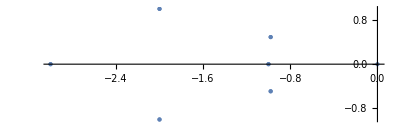

```mathematica
pts=Tc[Pρ,Pϕ] /. {H -> 1, R-> 1, W131-> 1,r->1, n-> 1, a-> 0.7};
ptsT = Transpose[pts];
ListPlot[ptsT,PlotStyle->PointSize[Large],AspectRatio->1/3]
```

## Problem 2

#### Enter in the expression for defocus wavefront aberration

```mathematica
Wdf = W020 ρ^2;
```

#### Find the defocus transverse ray aberration

```mathematica
Tdf[ρ_,ϕ_] = T[Wdf]
```

{-(2 R W020 ρ Sin[ϕ])/(n r),-(2 R W020 ρ Cos[ϕ])/(n r)}

### Part a

#### Enter the expression for spherical wavefront aberration

```mathematica
Ws = W040 ρ^4;
```

#### Find the spherical transverse ray aberration

```mathematica
Ts[ρ_,ϕ_] = T[Ws]
```

{-(4 R W040 ρ^3 Sin[ϕ])/(n r),-(4 R W040 ρ^3 Cos[ϕ])/(n r)}

#### Solve for where the sum of the spherical and defocus transverse ray aberration is zero

```mathematica
TpA[ρ_,ϕ_] = Tdf[ρ,ϕ] + Ts[ρ,ϕ];
```

```mathematica
SpA = Solve[TpA[0.7,0] == 0, W020];
```

```mathematica
SpA[[1,1]]
```

W020→-0.98 W040

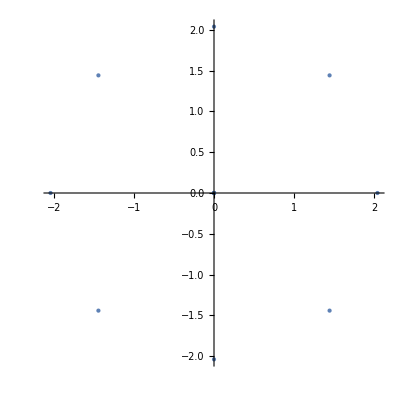

```mathematica
pts=TpA[Pρ,Pϕ] /. SpA[[1]] /. {H -> 1, R-> 1, W040-> 1,r->1, n-> 1, a-> 0.7};
ptsT = Transpose[pts];
ListPlot[ptsT,PlotStyle->PointSize[Large],AspectRatio->1]
```

### Part b.

#### Enter the expression for astigmatic wavefront aberration

```mathematica
Wa = W422 H^4 ρ^2 Cos[ϕ]^2;
```

#### Find the astigmatic transverse ray aberration

```mathematica
Ta[ρ_,ϕ_] = T[Wa]
```

{-(2 H^4 R W422 ρ Sin[ϕ])/(n r),0}

#### Solve for where the sum of the spherical and defocus transverse ray aberration is zero

```mathematica
TpB[ρ_,ϕ_] = Tdf[ρ,ϕ] + Ta[ρ,ϕ];
```

```mathematica
SpB = Solve[TpB[1.0,0] == 0, W020];
```

{{0,-1.41421,-2.,-1.41421,0,1.41421,2.,1.41421,-0.989949,-0.989949,0.989949,0.989949,0},{0.,0.,0,0.,0.,0.,0,0.,0.,0.,0.,0.,0}}

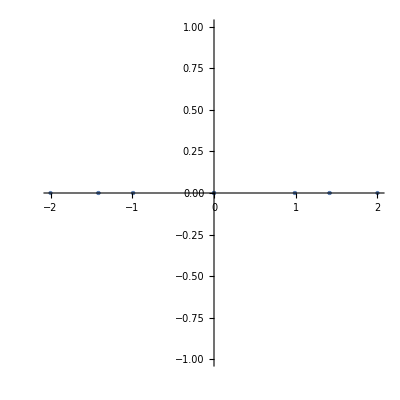

```mathematica
pts=TpB[Pρ,Pϕ]/.SpB[[1]] /. {H -> 1, R-> 1, W422-> 1,r->1, n-> 1, a-> 0.7}
ptsT = Transpose[pts];
ListPlot[ptsT,PlotStyle->PointSize[Large],AspectRatio->1]
```